```mathematica
Simplify[D[-((√z (-8 (-1+a) r^2 z+2 (-1+a) z^2+√(z (-r+z))-8 √(z^5 (-r+z))+16 a √(z^5 (-r+z))-8 a^2 √(z^5 (-r+z))+2 r (4 (-1+a) z^2+√(z (-r+z))+(-1+a) z (-1-4 √(z (-r+z))+4 a √(z (-r+z))))))/(√(-r+z) (-1-16 (-1+a)^2 r z+16 (-1+a)^2 z^2))),r]]
```

(√z (-2 (-r+z) (-1-16 (-1+a)^2 r z+16 (-1+a)^2 z^2) (-16 (-1+a) r z-z/(2 √(z (-r+z)))+(4 z^5)/(√(z^5 (-r+z)))-(8 a z^5)/(√(z^5 (-r+z)))+(4 a^2 z^5)/(√(z^5 (-r+z)))-(r z (1+4 (-1+a)^2 z))/(√(z (-r+z)))+2 (4 (-1+a) z^2+√(z (-r+z))+(-1+a) z (-1-4 √(z (-r+z))+4 a √(z (-r+z)))))-32 (-1+a)^2 z (-r+z) (-8 (-1+a) r^2 z+2 (-1+a) z^2+√(z (-r+z))-8 √(z^5 (-r+z))+16 a √(z^5 (-r+z))-8 a^2 √(z^5 (-r+z))+2 r (4 (-1+a) z^2+√(z (-r+z))+(-1+a) z (-1-4 √(z (-r+z))+4 a √(z (-r+z)))))-(-1-16 (-1+a)^2 r z+16 (-1+a)^2 z^2) (-8 (-1+a) r^2 z+2 (-1+a) z^2+√(z (-r+z))-8 √(z^5 (-r+z))+16 a √(z^5 (-r+z))-8 a^2 √(z^5 (-r+z))+2 r (4 (-1+a) z^2+√(z (-r+z))+(-1+a) z (-1-4 √(z (-r+z))+4 a √(z (-r+z)))))))/(2 (-r+z)^(3/2) (1+16 (-1+a)^2 r z-16 (-1+a)^2 z^2)^2)

```mathematica
Manipulate[Plot[%331,{r,0,2}],{a,4,8},{z,2,6}]
```

```mathematica
Solve[(a*x^ρ+b*y^ρ)^(1/ρ)== c,y]
```

{{y→(-(-c^ρ+a x^ρ)/b)^(1/ρ)}}

```mathematica
(-(-c^ρ+a x^ρ)/b)^(1/ρ)
```

```mathematica
(-(-c^ρ+a x^ρ)/b)^(1/ρ)
```

(-(-c^ρ+a x^ρ)/b)^(1/ρ)

```mathematica
Manipulate[Plot[(-(-c^ρ+a x^ρ)/b)^(1/ρ),{x,0,8}],{a,1,8},{b,1,2},{c,1,2},{ρ,-1,1}]
```

```mathematica
Manipulate[Plot[((1/c)^ρ-a x)/b,{x,0,8}],{a,1,8},{b,1,2},{c,1,2},{ρ,-1,1}]
```

```mathematica
Simple example
```

```mathematica
Solve[x(γ+(1-γ)(1-x/z))-p+k== 0,x]
```

{{x→-k+p}}

```mathematica
so f(x) is
```

```mathematica
(p-k)/z
```

```mathematica
So 1-F(x)
```

```mathematica
1-(p-k)/z== (z-p+k)/z
```

```mathematica
D[p*((z-p+k)/z)-k^2,k]== 0
```

-2 k+p/z==0

```mathematica
Solve[{D[p*((z-p+k)/z)-k^2,p]== 0,D[p*((z-p+k)/z)-k^2,k]== 0},{p,k}]
```

{{p→(2 z^2)/(-1+4 z),k→z/(-1+4 z)}}

```mathematica
Profit is:
```

```mathematica
Simplify[((2 z^2)/(-1+4 z))((z-((2 z^2)/(-1+4 z))+z/(-1+4 z))/z)-(z/(-1+4 z))^2]
```

z^2/(-1+4 z)

```mathematica
Cutoff:
```

```mathematica
x== p-k
```

```mathematica
Simplify[(2 z^2)/(-1+4 z)-(z/(-1+4 z))]
```

(z (-1+2 z))/(-1+4 z)

```mathematica
Simplify[Integrate[x-(z (1+2 z))/(-1+4 z),{x,(z (-1+2 z))/(-1+4 z),z}]+z^2/(-1+4 z)]
```

(z^2 (-1+2 z^2))/(1-4 z)^2

```mathematica
Simple example network only
```

```mathematica
Solve[x(1-x/z)-p+k== 0,x]
```

{{x→1/2 (z-√z √(4 k-4 p+z))},{x→1/2 (z+√z √(4 k-4 p+z))}}

```mathematica
Solve[{D[p(1-(1/(2*z) (z-√z √(4 k-4 p+z))))-k^2,p]==0,D[p(1-(1/(2*z) (z-√z √(4 k-4 p+z))))-k^2,k]==0},{p,k}]
```

{{p→((1+z) (1+4 z))/(18 z),k→(1+4 z)/(12 z)}}

```mathematica
Solve[{D[p(1-(1/(2*z) (z+√z √(4 k-4 p+z))))-k^2,p]==0,D[p(1+(1/(2*z) (z-√z √(4 k-4 p+z))))-k^2,k]==0},{p,k}]
```

{{p→0,k→0},{p→((1+z) (1+4 z))/(18 z),k→(1+4 z)/(12 z)}}

```mathematica
Simplify[(((1+z) (1+4 z))/(18 z))(1-(1/(2*z) (z+√z √(4 ((1+4 z)/(12 z))-4 ((1+z) (1+4 z))/(18 z)+z))))-((1+4 z)/(12 z))^2]
```

((1+4 z) (-3+12 z^2-4 √z √(2+1/z+z)-4 z^(3/2) √(2+1/z+z)))/(432 z^2)

```mathematica
Simplify[Integrate[x(1-(1/(2*z) (z+√z √(4 ((1+4 z)/(12 z))-4 ((1+z) (1+4 z))/(18 z)+z))))-((1+z) (1+4 z))/(18 z)+(1+4 z)/(12 z),{x,1/2 (z-√z √(4 (1+4 z)/(12 z)-4 ((1+z) (1+4 z))/(18 z)+z)),z}]+((1+4 z) (-3+12 z^2-4 √z √(2+1/z+z)-4 z^(3/2) √(2+1/z+z)))/(432 z^2)]
```

-((1+4 z) (3-9 z^2-6 z^3+4 √z √(2+1/z+z)+z^(3/2) √(2+1/z+z)+6 z^(5/2) √(2+1/z+z)))/(432 z^2)

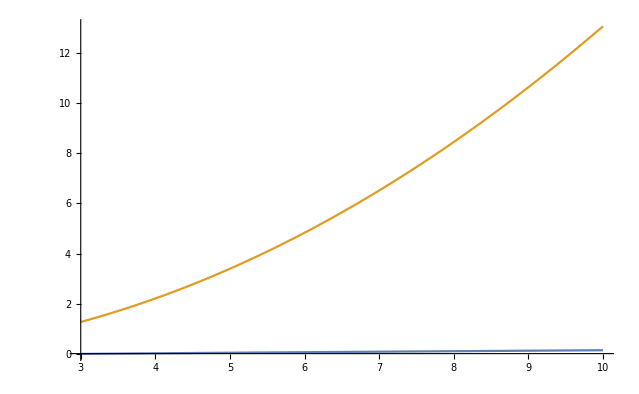

```mathematica
Plot[{-((1+4 z) (3-9 z^2-6 z^3+4 √z √(2+1/z+z)+z^(3/2) √(2+1/z+z)+6 z^(5/2) √(2+1/z+z)))/(432 z^2),(z^2 (-1+2 z^2))/(1-4 z)^2},{z,3,10}]
```

```mathematica
Comparison:=
```

```mathematica
Solve[{D[p((5-p+k)/5)-k^2,p]== 0,D[p((5-p+k)/5)-k^2,k]== 0},{p,k}]
```

{{p→50/19,k→5/19}}

```mathematica
Solve[{D[p(1-(1/(2*5) (5-√5 √(4 k-4 p+5))))-k^2,p]==0,D[p(1-(1/(2*5) (5-√5 √(4 k-4 p+5))))-k^2,k]==0},{p,k}]
```

{{p→7/5,k→7/20}}

```mathematica
Simplify[(z^2 (-1+2 z^2))/(1-4 z)^2+((1+4 z) (3-9 z^2-6 z^3+4 √z √(2+1/z+z)+z^(3/2) √(2+1/z+z)+6 z^(5/2) √(2+1/z+z)))/(432 z^2)]
```

(z^2 (-1+2 z^2))/(1-4 z)^2+((1+4 z) (3-9 z^2-6 z^3+4 √z √(2+1/z+z)+z^(3/2) √(2+1/z+z)+6 z^(5/2) √(2+1/z+z)))/(432 z^2)

```mathematica
For all z≥ than 1, this is positive.
```

```mathematica
Solve[x(γ+(1-γ)(1-x/z))-p+k== 0,x]
```

```mathematica
General case:=
```

{{x→(-z-√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ))},{x→(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ))}}

```mathematica
Distribution:=
```

```mathematica
(-z-√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)z)
1-((-z-√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)z))
```

```mathematica
(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)*z)
```

```mathematica
1-(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)*z)
```

```mathematica
Simplify[Solve[{D[p(1-((-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)*z)))-k^2,p]==0,D[p(1-((-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)*z)))-k^2,k]==0,k≥ 0,p≥ 0,z≥ 1,1≥ γ≥ 0,z^2-4 (k z-p z) (-1+γ)≥ 0,z≥ 1/(-1+2 γ)},{p,k}]]
```

{{p→ConditionalExpression[(-1+z^2 (-4-8 γ+8 γ^2)-√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))+z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))))/(36 z (-1+γ)),1/2<γ<1&&z>1/(-1+2 γ)],k→ConditionalExpression[-1/(24 z (-1+γ))(1+z^2 (1-2 γ)^2+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))-z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))-√(z^2 (17-20 γ+20 γ^2)+2 (1+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2)))-2 z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2)))))),1/2<γ<1&&z>1/(-1+2 γ)]},{p→ConditionalExpression[(-1+z^2 (-4-8 γ+8 γ^2)-√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))+z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))))/(36 z (-1+γ)),0<γ<1/2&&z>1],k→ConditionalExpression[-1/(24 z (-1+γ))(1+z^2 (1-2 γ)^2+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))-z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2))-√(z^2 (17-20 γ+20 γ^2)+2 (1+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2)))-2 z (-1+2 γ) (5+√(1+z (8-16 γ)+16 z^2 (1-γ+γ^2)))))),0<γ<1/2&&z>1]}}

```mathematica
D[p(1-((-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 (-1+γ)*z)))-k^2,γ]
```

p ((-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 z (-1+γ)^2)+(k z-p z)/(z √(z^2-4 (k z-p z) (-1+γ)) (-1+γ)))

```mathematica
(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 z (-1+γ)^2)+(k z-p z)/(z √(z^2-4 (k z-p z) (-1+γ)) (-1+γ))
```

(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 z (-1+γ)^2)+(k z-p z)/(z √(z^2-4 (k z-p z) (-1+γ)) (-1+γ))

```mathematica
Simplify[(-z+√(z^2-4 (k z-p z) (-1+γ)))/(2 z (-1+γ)^2)+(k z-p z)/(z √(z^2-4 (k z-p z) (-1+γ)) (-1+γ))]
```

(z-√(z (z-4 k (-1+γ)+4 p (-1+γ)))-2 k (-1+γ)+2 p (-1+γ))/(2 √(z (z-4 k (-1+γ)+4 p (-1+γ))) (-1+γ)^2)